```mathematica
(* 未经作者同意请不要复制或转载本文任何内容 *)
(* @By wuwc *)
(* @EMail: brucecen2@gmail.com *)
```

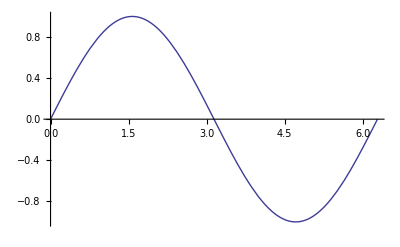

```mathematica
Plot[Sin[x], {x,0,2Pi}]
```

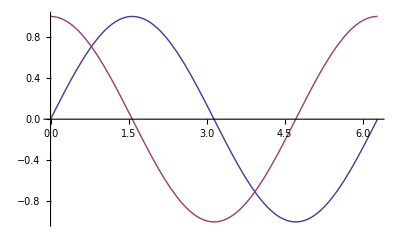

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2*Pi}]
```

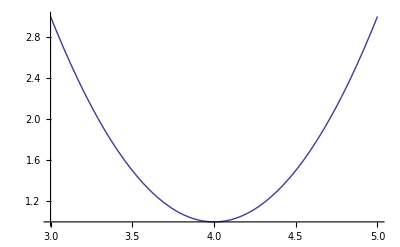

```mathematica
Plot [2*(x-4)^2+1, {x, 3, 5}]
```

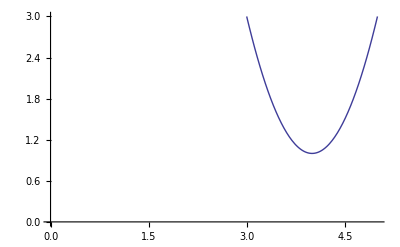

```mathematica
Plot[2*(x-4)^2+1,{x,3,5},AxesOrigin->{0,0}]
```

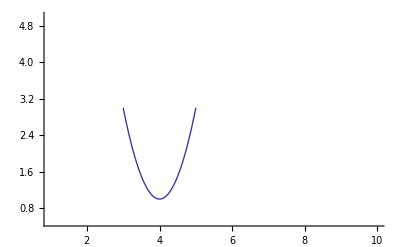

```mathematica
Plot[2*(x-4)^2+1,{x,3,5},AxesOrigin->{0,0}, PlotRange->{{1, 10}, {0.5, 5}}]
```

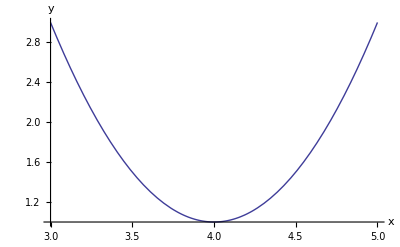

```mathematica
Plot[2*(x-4)^2+1, {x, 3, 5}, AxesLabel->{"x", "y"}]
```

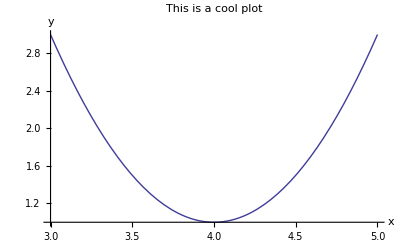

```mathematica
Plot[2*(x-4)^2+1, {x, 3, 5}, AxesLabel->{"x", "y"}, PlotLabel->"This is a cool plot", BaseStyle->{FontFamily->"DejaVu Sans Mono", FontSize->14}]
```

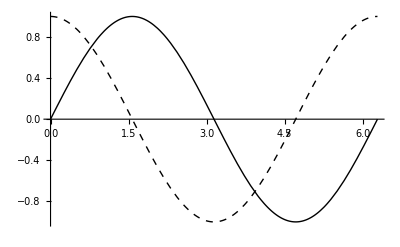

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2*Pi},
PlotStyle->{GrayLevel[0],{GrayLevel[0],Dashed}}]
```

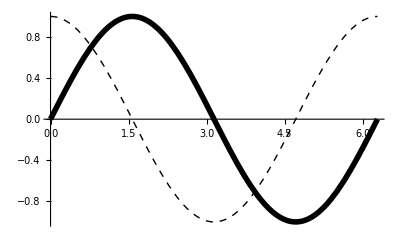

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2*Pi},
PlotStyle->{{GrayLevel[0], Thickness[0.01]},{GrayLevel[0],Dashed}}]
```

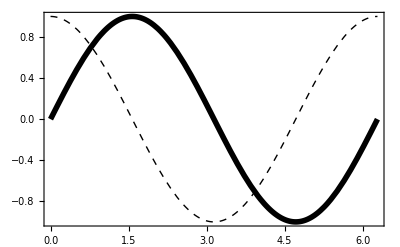

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2*Pi},
PlotStyle->{{GrayLevel[0], Thickness[0.01]},{GrayLevel[0],Dashed}},
Frame->True]
```

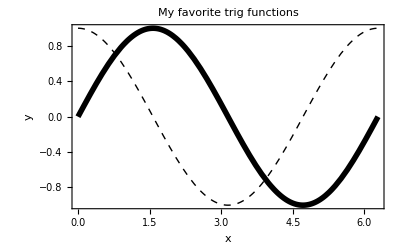

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2*Pi},
PlotStyle->{{GrayLevel[0], Thickness[0.01]},{GrayLevel[0],Dashed}},
Frame->True,
FrameLabel->{"x", "y"},
PlotLabel->"My favorite trig functions"]
```

```mathematica
$Packages
```

{ResourceLocator`,DocumentationSearch`,GetFEKernelInit`,JLink`,PacletManager`,WebServices`,System`,Global`}

```mathematica
<<PlotLegends`
```

```mathematica
$Packages
```

{PlotLegends`,ResourceLocator`,DocumentationSearch`,GetFEKernelInit`,JLink`,PacletManager`,WebServices`,System`,Global`}

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2*Pi},
PlotLegend->{"sin(x)", "cos(x)"}]
```

-Graphics-

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2*Pi},
PlotLegend->{"sin(x)", "cos(x)"},
LegendPosition->{1.1, -0.3}]
```

-Graphics-

```mathematica
a=2
b=3
a+b
a*b
a^b
```

2

3

5

6

8

```mathematica
a=2;
b=3;
a+b
a*b
a^b
```

5

6

8

```mathematica
x=2*a+b
```

7

```mathematica
Clear[a,x];
x
```

x

```mathematica
x=2*a+b
```

3+2 a

```mathematica
f[x_]:=2*(x-4)^2+1
```

```mathematica
?f
```

Global`f

f[x_]:=2 (x-4)^2+1

```mathematica
f[1]
```

19

```mathematica
f[Pi]
```

1+2 (-4+π)^2

```mathematica
N[f[Pi]]
```

2.47373

```mathematica
Plot[f[x], {x, 3, 5}]
```

-Graphics-

```mathematica
f[u_]:=4 Pi(M/(2Pi R T))^(3/2) u^2 E^(-M u^2/(2R T))
```

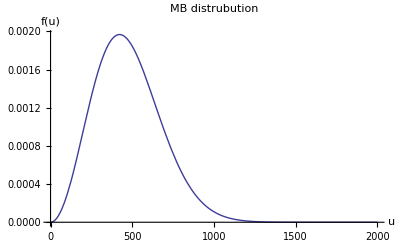

```mathematica
M=0.028;
T=300;
R=8.314;
Plot[f[u], {u, 0, 2000},
PlotLabel->"MB distrubution",
AxesLabel->{"u", "f(u)"}]
```

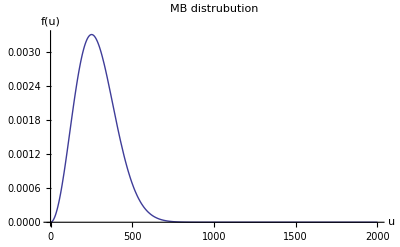

```mathematica
M=0.079;
Plot[f[u], {u, 0, 2000},
PlotLabel->"MB distrubution",
AxesLabel->{"u", "f(u)"}]
```

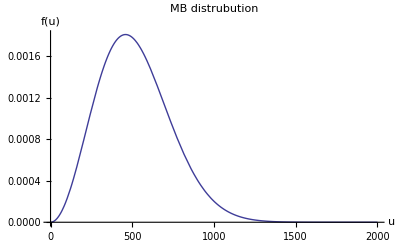

```mathematica
T=1000; 
Plot[f[u], {u, 0, 2000},
PlotLabel->"MB distrubution",
AxesLabel->{"u", "f(u)"}]
```

```mathematica
(* Homework *)
```

```mathematica
(* NULL *)
```